```mathematica
Quit[];
```

```mathematica
1+1//Timing
```

{6.×10^-6,2}

```mathematica
(*Here we will analyze P->kν using the modified SU(5) inspired MFV. Each dimension 6 BNV operator has had yukawas Subscript[Y, u] and Subscript[Y, d] inserted so as to be invariant under the flavor symmetry group Subscript[G, f] = SU Subscript[(3), 10] x SUSubscript[(3), 5]. So the matrix elements of the proton decay operators are all proportional to powers of the fermion yukawa couplings and ckm elements. We have calculated the inclusive decay rate, because no experiment can determine the flavor of the decay product neutrino*)
```

```mathematica
(*Constants used in proton decay rate, Subscript[ME, usd] are the hadronic matrix elements calculated on the lattice*)
mp = .938272;
mk = .493677;
hbar = 6.582122*10^-25;
MEusRdL = -0.049;
MEusLdL = 0.041;
MEudRsL = -0.134;
MEudLsL = 0.139;
MEdsLuL = 0.098;
CKM = {{.97417,.2248, 4.09*10^-3},{.220,.995,40.5*10^-3},{8.2*10^-3,40*10^-3,1.009}};
CKMdag = ConjugateTranspose[CKM];
(*Fermion masses and yukawa couplings at μ = 2 GeV*)
mcharm = 1.11;
mdown = .0049;
mup = .0024;
mstrange = .100;
v = 246;
ycharm = 2^(1/2)(mcharm/v);
ydown = 2^(1/2)(mdown/v);
yup = 2^(1/2)(mup/v);
ystrange = 2^(1/2)(mstrange/v);
```

```mathematica
<<"/Users/noahsteinberg/Physics/James_Research/Proton_Decay/Codes/BNV_Mathematica_Programs/RunDec.m"
ALL[μ_]:= Module[{as5mt, as5mb, as4mb, as4p0},
as5mt = AlphasExact[0.1185, 91.1876,173.21, 5, 4];
as5mb = AlphasExact[0.1185,91.1876,4.18,5,4];
as4mb = DecAsDownMS[as5mb, 4.18, 4.18, 4, 4];
as4p0 = AlphasExact[as4mb, 4.18, μ, 4, 4];
Return[(as4p0/as4mb)^(6/25)(as5mb/0.1185)^(6/23)((as4p0 + (50π)/77)/(as4mb + (50π)/77))^(-2047/11550)((as5mb + (23π)/29)/(0.1185 + (23π)/29))^(-1375/8004)];]
ALR[μ_]:= Module[{as5mt, as5mb, as4mb, as4p0},
as5mt = AlphasExact[0.1185, 91.1876,173.21, 5, 4];
as5mb = AlphasExact[0.1185,91.1876,4.18,5,4];
as4mb = DecAsDownMS[as5mb, 4.18, 4.18, 4, 4];
as4p0 = AlphasExact[as4mb, 4.18, μ, 4, 4];
Return[(as4p0/as4mb)^(6/25)(as5mb/0.1185)^(6/23)((as4p0 + (50π)/77)/(as4mb + (50π)/77))^(-173/825)((as5mb + (23π)/29)/(0.1185 + (23π)/29))^(-430/2001)];]
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

AlphasExact::shdw: Symbol AlphasExact appears in multiple contexts {RunDec`,Global`}; definitions in context RunDec` may shadow or be shadowed by other definitions.

DecAsDownMS::shdw: Symbol DecAsDownMS appears in multiple contexts {RunDec`,Global`}; definitions in context RunDec` may shadow or be shadowed by other definitions.

```mathematica
ALL[2]
```

1.25518

```mathematica
ALR[2]
```

1.25161

```mathematica
Γ[C1_,C2_, C3_, C4_, C5_,Λ_] :=((86400*365)/hbar) mp/(32π)(1 - mk^2/mp^2)^2((C1/Λ^2 yup*ystrange*CKM[[2,1]]*MEdsLuL*ALL[2]  + C2/Λ^2 yup*ystrange*CKM[[2,1]]*MEusLdL*ALL[2]  +C3/Λ^2 yup*ystrange*CKM[[2,1]]*MEdsLuL*ALL[2] + C4/Λ^2 yup*ystrange*CKM[[2,1]]*MEudLsL*ALL[2])^2  (*Subscript[ν, e] part*)
+(C1/Λ^2 yup*ystrange*CKM[[2,2]]*MEdsLuL*ALL[2]  + C2/Λ^2 yup*ystrange*CKM[[2,2]]*MEusLdL*ALL[2]  +C3/Λ^2 yup*ystrange*CKM[[2,2]]*MEdsLuL*ALL[2] + C4/Λ^2 yup*ystrange*CKM[[2,2]]*MEudLsL*ALL[2]+
C5/Λ^2 MEusRdL*ALR[2])^2 (*Subscript[ν, μ] part*)
+(C1/Λ^2 yup*ystrange*CKM[[2,3]]*MEdsLuL*ALL[2]  + C2/Λ^2 yup*ystrange*CKM[[2,3]]*MEusLdL*ALL[2]  +C3/Λ^2 yup*ystrange*CKM[[2,3]]*MEdsLuL*ALL[2] + C4/Λ^2 yup*ystrange*CKM[[2,3]]*MEudLsL*ALL[2])^2 (*Subscript[ν, τ] part*)
);
```

```mathematica
τ[a_,b_, c_, d_, e_,Λ_]:= 1/Γ[a,b,c,d,e,Λ];
```

```mathematica
τ[0,0,0,0,1,10^15] (*Lamda should be roughly the geometric mean of Subscript[M, SUSY] and Subscript[M, GUT]*)
```

1.13692×10^33

```mathematica
lifetime = LogLogPlot[τ[0,0,0,0,1,Λ], {Λ, 10^15, 10^16}];
```

```mathematica
lowerlimit a = LogLogPlot[y = 6*10^33, {x, 10^15, 10^16}, PlotLegends->{"SK Lower limit: 6*10^33"}, PlotStyle->Red];
```

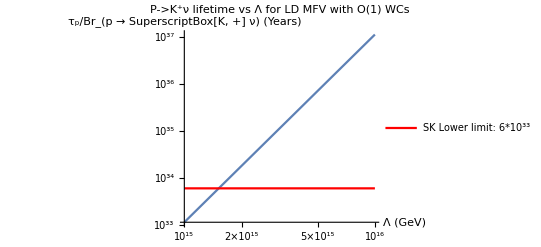

```mathematica
Show[lifetime,lowerlimit a,PlotRange->All, AxesLabel->{Style["Λ (GeV)",Black, 16],Style["τ_p/Br_(p → SuperscriptBox[K, +] ν) (Years)", Black, 16]}, TicksStyle->Large, PlotLabel->Style["P->K^+ν lifetime vs Λ for LD MFV with O(1) WCs", Black, 16]]
```

```mathematica
τ[.1,.1,.1,.1,.1,.1,10^12]
```

τ[0.1,0.1,0.1,0.1,0.1,0.1,1000000000000]

```mathematica
lifetime wilsons 9 = LogLogPlot[τ[0,0,0,0,C,10^14], {C, .001, 10}, PlotLegends->{"Λ = 10^14"}, PlotStyle->{Purple}];
lifetime wilsons 10 = LogLogPlot[τ[0,0,0,0,C,10^14.5], {C, .001, 10}, PlotLegends->{"Λ = 10^14.5"}, PlotStyle->{Red}];
lifetime wilsons 11 = LogLogPlot[τ[0,0,0,0,C,10^15], {C, .001, 10}, PlotLegends->{"Λ = 10^15"}, PlotStyle->{Blue}];
lifetime wilsons 12 = LogLogPlot[τ[0,0,0,0,C,10^15.5], {C, .001, 10}, PlotLegends->{"Λ = 10^15.5"}, PlotStyle->{Black}];
```

```mathematica
lowerlimit b = LogLogPlot[y = 6*10^33, {x, .001, 10}, PlotLegends->{"SK Lower limit: 6*10^33"}];
```

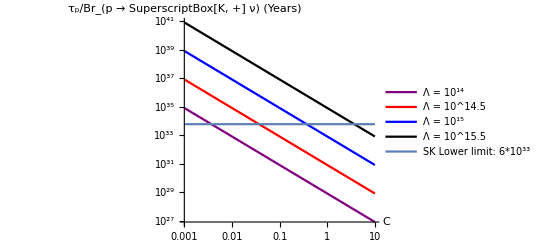

```mathematica
Show[lifetime wilsons 9,lifetime wilsons 10,lifetime wilsons 11,lifetime wilsons 12, lowerlimit b,PlotRange->All, AxesLabel->{Style["C",Black, 16],Style["τ_p/Br_(p → SuperscriptBox[K, +] ν) (Years)", Black, 16]}, TicksStyle->Large]
```

```mathematica
GrayLevel[0]
```

```mathematica
(*We can also imagine that the higher dimensional operators arise from integrating out particles in loops, thus they should each come with a factor of 1/(16 π^2)*)
```

```mathematica
Γ2[C1_,C2_, C3_, C4_, C5_,Λ_] :=((86400*365)/hbar) mp/(32π)(1 - mk^2/mp^2)((C1/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,1]]*MEdsLuL*ALL[2]  + C2/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,1]]*MEusLdL*ALL[2]  +C3/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,1]]*MEdsLuL*ALL[2] + C4/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,1]]*MEudLsL*ALL[2])^2  (*Subscript[ν, e] part*)
+(C1/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,2]]*MEdsLuL*ALL[2]  + C2/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,2]]*MEusLdL*ALL[2]  +C3/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,2]]*MEdsLuL*ALL[2] + C4/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,2]]*MEudLsL*ALL[2] + C5/(Λ*10^16*(16*π^2))MEusRdL*ALR[2])^2 (*Subscript[ν, μ] part*)
+(C1/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,3]]*MEdsLuL*ALL[2]  + C2/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,3]]*MEusLdL*ALL[2]  +C3/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,3]]*MEdsLuL*ALL[2] + C4/(Λ*10^16*(16*π^2))yup*ystrange*CKM[[2,3]]*MEudLsL*ALL[2])^2 (*Subscript[ν, τ] part*)
);
```

```mathematica
τ2[a_,b_, c_, d_, e_,Λ_]:= 1/Γ2[a,b,c,d,e,Λ];
```

```mathematica
τ2[1,1,1,1,.01,10^10]
```

2.05027×10^33

```mathematica
lifetime wilsons a = LogLogPlot[τ[C,C,C,C,C,10^12.5], {C, .001, 10}, PlotLegends->{"Λ = 10^12.5"}, PlotStyle->{Purple}];
lifetime wilsons b = LogLogPlot[τ[C,C,C,C,C,10^13], {C, .001, 10}, PlotLegends->{"Λ = 10^13"}, PlotStyle->{Red}];
lifetime wilsons c = LogLogPlot[τ[C,C,C,C,C,10^13.5], {C, .001, 10}, PlotLegends->{"Λ = 10^13.5"}, PlotStyle->{Blue}];
lifetime wilsons d = LogLogPlot[τ[C,C,C,C,C,10^14], {C, .001, 10}, PlotLegends->{"Λ = 10^14"}, PlotStyle->{Black}];
```

```mathematica
Show[lifetime wilsons a,lifetime wilsons b,lifetime wilsons c,lifetime wilsons d, lowerlimit b,PlotRange->All, AxesLabel->{Style["C_i",Black, 16],Style["τ_p/Br_(p → SuperscriptBox[K, +] ν) (Years)", Black, 16]}, TicksStyle->Large, PlotLabel->Style["P->K^+ν for LD MFV", Black, 16]]
```